# 运用概率论的知识造个星球 曹芷昕 中山大学计算机学院 22336023

## 1. 引言：

本学期我学习了mathematica编程与概率论，为了巩固知识与加深对知识点了理解，我结合了mathematica语言与概率论知识，参考了UCB CS126的lab[1]模拟沿海地区植被的生长和进化，并尝试了解生物进化如何受到基因类型、突变率、土地类型和其他变异因素的影响。为此，我们将建立一个世界，并将植物视为粒子。在每个时间单位内，这些植物将相互繁殖，争夺有限的空间，并在此过程中传递更适合的基因。

## 2. 问题定义

我们创造了一个世界，这个世界有 7 种地形：海洋（ocean）、浅滩（shallows）、海滩（beach）、沼泽（dirt）、内陆（inland）、高山（mountain）以及雪山（snow）。其中雪山和海洋不能生长植物，但顽强的种子可以在这海洋中传播。其他各自地形都有最适合的植物。适合的植物种类与土壤种类如下
-Graphics-
图片源自[1]
一个世界有许多块土地，我们用“方块”来指代一个土地。一个土地上最多只能有一棵树木，以及可能有若干棵种子。这些植物（种子和树木）会竞争这片土地。每个时间单位，每个方块上的植物会根据适应程度进行竞争，决定谁能生存下来，并决定谁能长成大树。
每个植物（树木或种子）都有一个 DNA，其中包含 5 个数值，加起来等于 1。这 5 个数值分别对应该植物在 5 种地形中的适应情况。数值最大的地形索引表示该植物最适合生长在哪种地形。例如，DNA 为 [0.2, 0.3, 0.1, 0.4, 0.0] 的树木最适合在内陆中生长。每个时间单位，树木都有一定概率生下种子。

## 2. 项目实现：

1.造块大陆：
理论基础：柏林噪音。为了生成一个自然的世界，使用柏林噪音柏林噪声是一个非常强大算法，经常用于程序生成随机内容，在游戏和其他像电影等多媒体领域广泛应用。柏林噪声可以用于生成波形，起伏不平的材质或者纹理。例如，它能用于程序生成地形，火焰燃烧特效，水和云等等比如下：
-Graphics-
本程序的柏林噪音的实现参考了
[1]https://inst.eecs.berkeley.edu/~ee126/fa23/labs/lab3.zip,
[2]https://adrianb.io/2014/08/09/perlinnoise.html,
[3]https://www.youtube.com/watch?v=kCIaHqb60Cw&ab_channel=Zipped
运用的概率论知识：无

```mathematica
(*生成梯度向量，向量的分量坐标x_i符合分布。输入:n: 向量的维度。输出：一个n维的梯度向量*)
generateGradient[n_] := Module[
{grad = RandomVariate[NormalDistribution[0, n], n]},
grad/Norm[grad]]
```

```mathematica
(*给定层数l，生成的2维的梯度向量。*)
generateCornerGradient[l_] := 
Module[{corners = Table[generateGradient[2], {i, 1, (l+1) (l+1)}]},
ArrayReshape[corners, {l+1, l+1, 2}]]
```

```mathematica
(*给定(x,y)以及附近的整数点(ix,iy)以及梯度向量矩阵计算(ix,iy)点的梯度向量和(x-ix, y-iy)之间的点积*)
dotGridGradient[ix_, iy_, x_, y_, mat_] :=
Module[{grad = Indexed[mat, {ix, iy}], dx = x - ix, dy = y - iy},
Dot[grad, {dx, dy}]]
```

```mathematica
(*以下两个函数用于插值，目的是让图像变化看起来更自然*)
fade[t_] := 6 t^5-15 t^4+10 t^3
```

```mathematica
Interp[t_,  a_, b_] := (1 - fade[t]) a + fade[t] b
```

```mathematica
(*函数接受(x,y)坐标和一个之前生成的梯度向量集作为参数，返回该点的灰度，*)
perlin[x_, y_, mat_] := 
Module[{weightX = x - Floor[x], weightY = y- Floor[y], len = Length[mat]},
Interp[weightY,Interp[weightX, dotGridGradient[Floor[x], Floor[y],x, y, mat], dotGridGradient[Min[Floor[x]+1,len],  Floor[y], x, y, mat]], Interp[weightX, dotGridGradient[Floor[x], Min[Floor[y]+1,len] ,x, y, mat], dotGridGradient[Min[Floor[x]+1, len], Min[Floor[y]+1,len], x, y, mat]]
]
]
```

```mathematica
(*对每个pixel进行操作，利用倍频实现更自然的噪声。给定层数（此处的os),计算os层柏林噪音叠加，之后再乘一个参数放大每个点之间灰度的区别*)
actionPerPixel[x_, y_, mat_, os_] := 
Module[{val = 0, amp, freq, logF},
For[logF = 0, logF < os, logF++, freq = 2^logF; amp = 1/freq;val += perlin[x freq + 1.0, y  freq + 1.0, mat]* amp; ];
val *= 2^0.5
]
```

```mathematica
(*辅助函数，生成n个平均再[a,b]区间的数。*)
linearmesh[a_,b_,n_Integer]:=Array[#&,n,{a,b}]
```

```mathematica
(*给定的生成图片的大小size和l层数，生成一张柏林噪音图片*)
FullPerlin[size_, l_] := Module[
{grad = generateCornerGradient[2^l], units = linearmesh[0, 1, size]},
 Table[ actionPerPixel[x, y, grad, l], {y, units}, {x, units}]
]
```

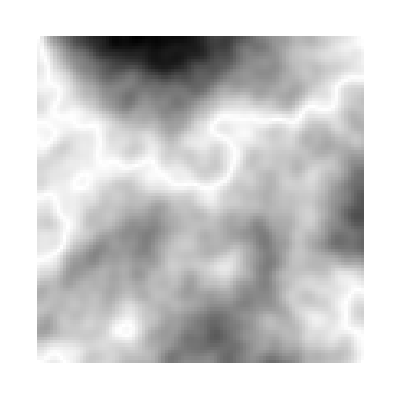

```mathematica
(*尝试生成一个100x100大小，层数为5的柏林噪音*)
array = FullPerlin[100, 5];
ArrayPlot[array]
```

好的，现在我们随机生成了一个自然世界，现在让我们加上地形的划分。（颜色以及对应地形的概率参考了[1])

```mathematica
(*以下数据参考了[1]*)
treeColors={{104/256,230/256,158/256},{114/256,134/256,38/256},{70/256,126/256,4/256},{42/256,70/256,8/256},{142/256,170/256,72/256}};
groundColors={{65/256,105/256,225/256},{51/256,230/256,255/256},{238/256,214/256,175/256},{160/256,82/256,45/256},{139/256,69/256,19/256},{139/256,137/256,137/256},{255/256,250/256,250/256}};
idealColors={{65/256,105/256,225/256},{104/256,230/256,158/256},{114/256,134/256,38/256},{70/256,126/256,4/256},{42/256,70/256,8/256},{142/256,170/256,72/256},{255/256,250/256,250/256}};
exampleFitness={0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
groundElevations={0.01,0.075,0.15,0.2,0.3,0.4,1.0};
hO={0,0.5,0.05};
h={0,0.5,0.05};
r={0.0,1};
```

```mathematica
(*以下数据参考了[1]*)
idealRule={1->RGBColor[65/256,105/256,225/256],2->RGBColor[104/256,230/256,158/256],3->RGBColor[114/256,134/256,38/256],4->RGBColor[70/256,126/256,4/256],5->RGBColor[42/256,70/256,8/256],6->RGBColor[142/256,170/256,72/256],7->RGBColor[255/256,250/256,250/256]}
groundRule = {1->RGBColor[65/256,105/256,225/256],2->RGBColor[51/256,230/256,255/256],3->RGBColor[238/256,214/256,175/256],4->RGBColor[160/256,82/256,45/256],5->RGBColor[139/256,69/256,19/256],6->RGBColor[139/256,137/256,137/256],7->RGBColor[255/256,250/256,250/256]}
treeRule = {1->RGBColor[104/256,230/256,158/256],2->RGBColor[114/256,134/256,38/256],3->RGBColor[70/256,126/256,4/256],4->RGBColor[42/256,70/256,8/256],5->RGBColor[142/256,170/256,72/256]
}
{1->RGBColor[Rational[13, 32], Rational[115, 128], Rational[79, 128]],2->RGBColor[Rational[57, 128], Rational[67, 128], Rational[19, 128]],3->RGBColor[Rational[35, 128], Rational[63, 128], Rational[1, 64]],4->RGBColor[Rational[21, 128], Rational[35, 128], Rational[1, 32]],5->RGBColor[Rational[71, 128], Rational[85, 128], Rational[9, 32]]}
```

{1→RGBColor[Rational[65, 256], Rational[105, 256], Rational[225, 256]],2→RGBColor[Rational[13, 32], Rational[115, 128], Rational[79, 128]],3→RGBColor[Rational[57, 128], Rational[67, 128], Rational[19, 128]],4→RGBColor[Rational[35, 128], Rational[63, 128], Rational[1, 64]],5→RGBColor[Rational[21, 128], Rational[35, 128], Rational[1, 32]],6→RGBColor[Rational[71, 128], Rational[85, 128], Rational[9, 32]],7→RGBColor[Rational[255, 256], Rational[125, 128], Rational[125, 128]]}

{1→RGBColor[Rational[65, 256], Rational[105, 256], Rational[225, 256]],2→RGBColor[Rational[51, 256], Rational[115, 128], Rational[255, 256]],3→RGBColor[Rational[119, 128], Rational[107, 128], Rational[175, 256]],4→RGBColor[Rational[5, 8], Rational[41, 128], Rational[45, 256]],5→RGBColor[Rational[139, 256], Rational[69, 256], Rational[19, 256]],6→RGBColor[Rational[139, 256], Rational[137, 256], Rational[137, 256]],7→RGBColor[Rational[255, 256], Rational[125, 128], Rational[125, 128]]}

{1→RGBColor[Rational[13, 32], Rational[115, 128], Rational[79, 128]],2→RGBColor[Rational[57, 128], Rational[67, 128], Rational[19, 128]],3→RGBColor[Rational[35, 128], Rational[63, 128], Rational[1, 64]],4→RGBColor[Rational[21, 128], Rational[35, 128], Rational[1, 32]],5→RGBColor[Rational[71, 128], Rational[85, 128], Rational[9, 32]]}

{1→RGBColor[Rational[13, 32], Rational[115, 128], Rational[79, 128]],2→RGBColor[Rational[57, 128], Rational[67, 128], Rational[19, 128]],3→RGBColor[Rational[35, 128], Rational[63, 128], Rational[1, 64]],4→RGBColor[Rational[21, 128], Rational[35, 128], Rational[1, 32]],5→RGBColor[Rational[71, 128], Rational[85, 128], Rational[9, 32]]}

```mathematica
(*给定一个数字（海拔），计算出他属于哪个地形*)
findBucket[elevation_]:= Module[{index = 1, hb = {0.01,0.075,0.15,0.2,0.3,0.4,1.0}},
While[elevation > hb[[index]] ,index+=1];
index
]
```

```mathematica
(*给定一个矩阵，计算出他的地形类型矩阵*)
getUninhabitedWorld[grid_]:= 
Table[findBucket[Indexed[grid, {i, j}]], {i, 1, Length[grid]}, {j,1, Length[grid]}]
```

```mathematica
(*给定一个矩阵，计算出他的地形类型对应的颜色（用{r,g,b}表示）的矩阵*)
getUninhabitedWorld2[grid_]:= 
Table[Indexed[groundColors,findBucket[Indexed[grid, {i, j}]]], {i, 1, Length[grid]}, {j,1, Length[grid]}]
```

```mathematica
(*给定一个矩阵，计算出他的地形类型对应的植物的颜色（用{r,g,b}表示，如果该地方不能生长植物则该方块用土地的颜色表示）的矩阵*)
getIdealWorld[grid_] := Table[Indexed[idealColors,findBucket[Indexed[grid, {i, j}]]], {i, 1, Length[grid]}, {j,1, Length[grid]}]
```

```mathematica
(*展示原始世界以及生长了理想植物的世界的函数,展现光栅是与arrayplot不同，会发生旋转*)
```

```mathematica
displayUnhabitedWorld[grid_] :=Graphics[Raster[getUninhabitedWorld2[grid]]]
displayIdealWorld[grid_]:= Graphics[Raster[getIdealWorld[grid]]]
```

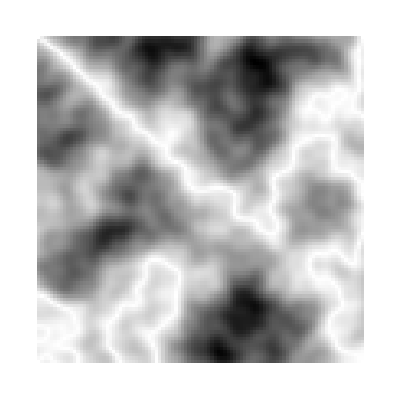
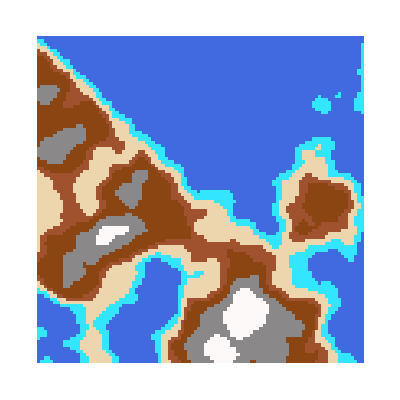
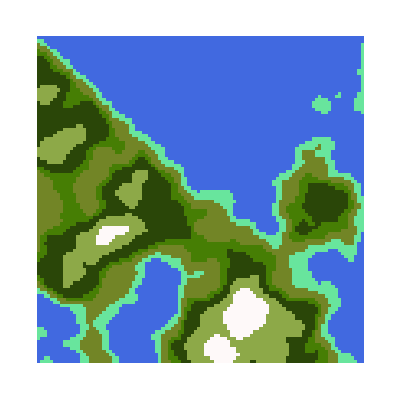
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*同时展示柏林噪音图以及它对应的等高图、原始世界和理想世界（从左到右,同时也展示了光栅的旋转，第3，5张图是用根据光栅作图)*)
Module[{grid = FullPerlin[100,5]},
{ArrayPlot[grid],ArrayPlot[getUninhabitedWorld[grid]],displayUnhabitedWorld[grid],ArrayPlot[getUninhabitedWorld[grid], ColorRules->groundRule],
displayIdealWorld[grid],ArrayPlot[getUninhabitedWorld[grid],ColorRules->idealRule]}]
```

### 2. 种棵树吧

理论基础：生物的遗传与变异
概率论知识在此处的运用：
·1. 生成随机树：假定随机生成的树（没有父母的树）的dna每个基因X_i符合均匀分布X_i~U（0，1）(i=1,2,3,4,5)，最后我们再对dna处理使dna中基因之和等于1（实现在randomDNA中）
2.  生成随机后代：棵树的后代(种子)的DNA可能会发生轻微的突变。这种突变在父母的DNA载体上增加了一个小的扰动载体。摄动向量的每个入口均匀地从[−φ，φ]中采样（φ=mutationVar)（实现在genOffspring中）
注：此处开始运用了面向对象编程的方法，参考了[4]https://12000.org/my_notes/object_based_in_mathematica/index.htm

```mathematica
TreeClass[$dna_] :=
Module[{dna, self, randomDNA},
SetAttributes[self, HoldAll];
(*------------------ private methods -----------------------------*)
(*假定随机生成的树（没有父母的树）的dna每个基因符合均匀分布（0，1），最后我们再对dna处理使dna中基因比重之和等于*)
randomDNA[] := Module[{randDNA = Table[RandomVariate[UniformDistribution[{0, 1}]],5]},
randDNA/Total[randDNA]];
(*------------------ public methods -----------------------------*)
self@genOffspring[mutationVar_] := 
(*棵树的后代(种子)的DNA可能会发生轻微的突变。这种突变在父母的DNA载体上增加了一个小的扰动载体。摄动向量的每个入口均匀地从[−φ，φ]中采样。*)
Module[{offSpringDNA =Map[Function[x,  Clip[x, {0, 1}]],Table[RandomVariate[UniformDistribution[{-mutationVar, mutationVar}]], 5]+dna]}, TreeClass[offSpringDNA /Total[offSpringDNA]]
];
self@getColor[]:= Dot[dna, treeColors];
self@getDNA[]:= dna;
(*最合适的位置：最大的基因所在的索引*)
self@preferLocation[]:= Ordering[dna, -1];
(*fitness：如果类型为1（即ocean)则为shallows的基因比重，如果是6（snow）,则为0，什么都不适合长在雪山上，如果在1，2，3，4，5，则为对应的基因的比重*)
self@calcFitness[envType_]:= If[envType === 0, dna[[1]], If[envType === 6, 0, Indexed[dna,envType]]];
(*------------------------ constructor code --------------------------*)
dna = If[$dna=== None, randomDNA[], $dna];
self
];
```

```mathematica
visualizeDNA[tree_] := Module[
{bar = BarChart[tree@getDNA[],ChartStyle->{1,2,3,4,5}/.treeRule,  AxesLabel->{Style["Environment Type",Bold], Style["SurvivalProbability"]},PlotLabel->"DNA  Visualization",PlotRange->{All, {0, 1}}],fig = Graphics[Raster[{{tree@getColor[]}}], PlotLabel->"Resultant Tree Color"]},
GraphicsRow[{Image[bar], fig}]]
```

```mathematica
tree = TreeClass[None];
```

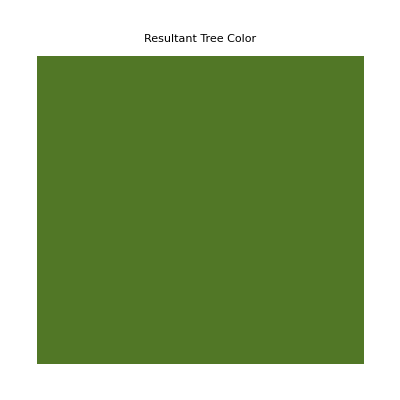

```mathematica
visualizeDNA[tree]
```

```mathematica
(*该模块实现了的树木繁殖基因变化的展示（在没有自然选择作用下）*)
DynamicModule[{tree = TreeClass[None],var = 0.01,i= 0,temp},Dynamic[If[i === 50,i=50;visualizeDNA[tree],i++;temp=tree;tree=tree@genOffspring[var];visualizeDNA[temp]],UpdateInterval->0.1]]
```

### 3.哦，不！过度繁殖，他们打起来了！

理论基础：自然选择
概率论知识在此处的运用：
·1.树木的生成：你的世界一开始是空的，但在每一个时间步骤中，一棵树会神奇地出现在一个正方形中。也许是通过动物带来的种子。这将在simulate_life_creation中实现。
2.树木的死亡：如果tree当前在一个正方形中，它以一定的概率存活于每一个时间步。这在age_tree中实现
3.树木的繁殖：如果它存活下来，它也可以产生许多后代。子代的数量符合X~B(𝑛=self.max_seeds, p=fitness)
4.树木的竞争：运用了玻尔兹曼分布，如果一堆树在同一个方块上，它们会因为资源有限而竞争这个方块！每棵树t在广场上s
有一个“能量”值等于exp(self.comp_constant⋅.fitness)， 然后，方块上的每棵树都以与其能量值成比例的概率获胜。这在sample_boltzmann_distribution中实现。

```mathematica
(*方块：height：高度，soilColor：泥土颜色，mutationVar:变异偏差，compConst:competeConstant竞争常数，lifeProb:适宜生命的程度（产生新生命的概率与树的存活概率相关），maxSeed：该方块能产生的最大种子数量*)
squareClass[$height_, $soilColor_, $mutationVar_, $traitsDim_, $compConst_, $lifeProb_, $maxSeed_] :=
Module[{traitsDim, soilColor,envType, mutationVar, maxSeeds, lifeProb, compConst, tree, seeds, futureSeed, self, sampleBoltzDistr,simulateLifeCreation,ageTree, terminateTree, ageSeeds, fitnessComp},
SetAttributes[self, HoldAll];
(*------------------ private methods -----------------------------*)
(*input：fitness：一个包含所有树的适应程度的数组，returnDist:如果为真，则返回一个包含所有树存活概率的数组，否则返回所有树中争夺胜利者的index
模拟方块上的树竞争方块资源：因为一个方块上的资源是有限的，所以在这个方块的树会争夺这个方块的资源，这个函数用于计算每棵树争夺胜利的概率。运用玻尔兹曼分布计算：方块上每一棵树的既有能量Exp[compConstant*fitness],即e的竞争程度与自己的适应程度乘积次方，而方块上的每棵树获胜的概率与其能量值成正比。。*)
sampleBoltzDistr[fitness_, returnDist_] :=Module[{energy = Exp[compConst fitness],prob},prob = energy/Total[energy];If[returnDist, prob, RandomChoice[prob->Table[i, {i, 1, Length[fitness]}]]]];
(*模拟新生命的产生：如果当前方块是空的，那么该方块又lifeProb概率产生新生命*)
simulateLifeCreation:= If[RandomVariate[UniformDistribution[{0, 1}]]<lifeProb,self@plantSeed[TreeClass[None]],Return];
(*模拟生命的终结：如果当前方块上有树，那么它又1-survivalProb概率死掉*)
ageTree[]:=Module[{survivalProb},If[self@containtree[], survivalProb = tree@calcFitness[envType], Return[]];
If[RandomVariate[UniformDistribution[{0, 1}]]>survivalProb,terminateTree, Return[]]];

terminateTree[]:= Clear[tree];tree = None;

(*模拟种子的存活情况：因为种子存活概率会随时间递减，所以要移除死掉的种子*)
ageSeeds[]:=seeds = Select[seeds,Function[{tree}, RandomVariate[UniformDistribution[{0, 1}]]<tree@calcFitness[envType]]];
(*模拟方块上植物间的竞争情况，种子和树木都参与竞争，按照sampleBoltzDistr决出胜者*)
fitnessComp[]:=Module[
{competitors = seeds,fitness,weightedFitness,winIndex},
If[self@containtree[],AppendTo[competitors, tree ],None];
If[Length[competitors]==0,Return[], None];
fitness = Table[Indexed[competitors, i]@calcFitness[envType],{i, 1, Length[competitors]}];
weightedFitness =compConst fitness;weightedFitness=(weightedFitness- Max[weightedFitness])/compConst;
winIndex = sampleBoltzDistr[fitness, False];
tree = competitors[[winIndex]];];
(*--------------------public methods--------------------------------*)
self@isOcean[] := (envType === 0);
self@containtree[] := Not[tree ===None];

self@isHabitable[] := MemberQ[Table[i, {i, 0,5}], envType];
(*生成方块中树木的后代*)
self@genOffspring[]:=Module[
{fitness, numOfSpring},
If[Not[self@containtree[]],Return [{}],fitness = tree@calcFitness[envType]];
numOfSpring = RandomVariate[BinomialDistribution[maxSeeds,fitness]];
Table[tree@genOffspring[mutationVar],{i, 1, numOfSpring}]];
self@envStep[]:=(
simulateLifeCreation[];
If[self@isHabitable[],(ageTree[];fitnessComp[];), ageSeeds[]];
seeds = futureSeed;
futureSeed={};
);
self@plantSeed[seed_] := (futureSeed = Append[futureSeed, seed];);
(*计算当前的方块上生长的树木是否最符合当前地形*)
self@convergence[]:=If[self@containtree[], If[Indexed[tree@preferLocation[],1]===envType,1,0],0];
(*计算当前方块的树木对该方块的适应程度*)
self@fitness[]:=If[self@containtree[], tree@calcFitness[envType],0];
self@getSquareColor[]:=If[self@containtree[],tree@getColor[],soilColor];
self@getTree[]:=tree;
self@setTree[ttree_]:=tree =ttree;
(*获取新的种子，如果这里是海，移除当前的种子，并返回当前的种子*)
self@getSeeds[]:=Module[{returnSeed},
If[self@isOcean[],(returnSeed=seeds;seeds={};),returnSeed = self@genOffspring[]];
returnSeed];
(*------------------------ constructor code --------------------------*)
traitsDim = $traitsDim;
soilColor = $soilColor;
envType = findBucket[$height]-1;
mutationVar = $mutationVar;

maxSeeds = $maxSeed;
lifeProb = $lifeProb;
compConst = $compConst;
tree = None;
seeds = {};
futureSeed = {};

self
];
```

```mathematica
createDirtSquare[var_, compConst_]:=
squareClass[0.2, {0,0,0}, var, 5, compConst, 1, 10]
```

```mathematica
(* 下面该模块植物在沼泽中的竞争，期间程序可能会报错，原因是dna中间的数字经过计算后，相差太大了，部分精度会丢失*)
```

```mathematica
DynamicModule[{square = createDirtSquare[0.6,10], i = 0},Dynamic[If[i === 50,i = 50;visualizeDNA[square@getTree[]], i++;square@envStep[];Table[square@plantSeed[c], {c, square@genOffspring[]}];If[square@containtree[], None, square@setTree[TreeClass[None]]];visualizeDNA[square@getTree[]],UpdateInterval->2]]]
```

下面图片为2023/11/27/22：02模拟图片：竞争常数：1000，变异率0.03

竞争常数100，变异率0.03-Graphics-

竞争常数10，变异率0.03-Graphics-

竞争常数10，变异率0.6，基因在20步内达到只有一种基因，之后又继续变异产生如下结果
-Graphics-

可以看出竞争常数越大，收敛越快，当这个常数很高时，拥有更好的适应性就变得越来越重要。这导致DNA分布一旦收敛，随着时间的推移，变异很小。同样，当竞争常数较低时，DNA分布的变化就会很高，因为其他树更有可能存活下来。
而突变方差能加快收敛速度，但在收敛过程在非常高的时候更加易变，在较低的时候更加缓慢和稳定。一旦达到稳定状态，高突变方差意味着会有更多偏离最佳适应度的变异。所以，在一个快速变化的环境中，我们想要一个高突变方差，这样我们才能跟上变化。对于一个更可预测的环境，我们想要一个低突变方差，这样我们就可以稳定地收敛并保持在那里。

### 4.世界！世界！

概率论知识在此处的运用：
1.植物种子的传播：种子从(x,y)传播到其他方块，传播的方块的位置符合正态分布，即x’~N(x,var),y’~(y,var),然后对(x’,y’)进行处理，确保它在方块范围中且为整数，这实现在simulate_movement中；
var的控制，海洋则为waves_var,其他则为wind_var，实现在spread_seeds中
注：此处运用了面向对象编程的方法，参考了[4]https://12000.org/my_notes/object_based_in_mathematica/index.htm
不错，完成了，直到我跑了最后的模拟程序。。。

```mathematica
worldClass[  $dim_, $mutationVar_,$windVar_, $wavesVar_, $lifeProb_,$compConst_,$maxSeeds_]:= 
Module[{square, dim, lifeProb, compConst,traitsDim,mutationVar, windVar, wavesVar,maxSeeds,traitGrid,colorGrid, idealGrid,initialWorld, world, fitnessProgress, spreadProg,convergenceProg,timeStep,self,simulateMoveent,spreadSeed,initializeWorld, stepSquare,updateStatistics},SetAttributes[self, HoldAll];
(*------------------ private methods -----------------------------*)
(*初始化世界的所有方块*)
initializeWorld[]:=Table[squareClass[Indexed[traitGrid,{x,y}],Indexed[colorGrid,{x,y}],mutationVar,traitsDim,compConst,lifeProb,maxSeeds], {x, 1, dim}, {y, 1, dim}];
(*计算每个方块进化*)
stepSquare[x_, y_, stats_]  :=Module[
{statsCopy = stats, sqre = Indexed[world,{x,y}]},
Indexed[world,{x,y}]@envStep[];
spreadSeed[x, y];
statsCopy["totalTrees"] += If[sqre@containtree[],1,0];
statsCopy["totalHabitable"] += If[And[sqre@isHabitable[],Not[sqre@isOcean[]]],1,0];
statsCopy["totalFitness"]+=sqre@fitness[];
statsCopy["totalConvergence"]+= sqre@convergence[];

statsCopy
];
(*stats用于数据记录*)
updateStatistics[stats_] := (

AppendTo[fitnessProgress, stats["totalFitness"]/Max[stats["totalTrees"]]];
AppendTo[spreadProg,stats["totalTrees"]/Max[stats["totalHabitable"]]]
;
AppendTo[convergenceProg,stats["totalConvergence"]/Max[stats["totalTrees"]]];
);
(*植物种子的传播：种子从(x,y)传播到其他方块，传播的方块的位置符合正态分布，即x'~N(x,var),y'~(y,var),然后对(x',y')进行处理，确保它在方块范围中且为整数，这实现在simulate_movement中；var的控制，海洋则为waves_var,其他则为wind_var，实现在spread_seeds中*)
simulateMoveent[x_,y_,var_]:=Module[
{coord,minVal = 1, maxVal = dim},Round[Clip[{RandomVariate[NormalDistribution[x, var]],RandomVariate[NormalDistribution[y,var]]},{minVal, maxVal}]
]
];
spreadSeed[x_, y_]:=Module[{sqre = Indexed[world,{x,y}],trees,var,coord},
trees = sqre@getSeeds[];
If[sqre@isOcean[],var=wavesVar,var=windVar];
Table[coord=simulateMoveent[x,y,var];Indexed[world,coord]@plantSeed[tree], {tree, trees}];
];


(*------------------ public methods -----------------------------*)
self@envStep[] := Module[
{stats = <|"totalTrees"->0, "totalHabitable"->0, "totalFitness"->0, "totalConvergence"->0|>},
(*self@displayVisuals[];*)
Table[stats=stepSquare[m,n,stats],{m, 1, dim},{n, 1, dim}];
colorGrid = Table[Indexed[world,{m, n}]@getSquareColor[],{m,1,dim},{n,1,dim}];
stats=updateStatistics[stats];
timeStep+=1;
];

self@getuhhtdWorld[]:=initialWorld;
self@getIdlWorld[]:=idealGrid;
self@getCurrWorld[]:=colorGrid;
self@getGrid[]:=world;
self@getProg[]:={fitnessProgress,spreadProg,convergenceProg};
self@displayWorld[]:=GraphicsRow[{Labeled[displayUnhabitedWorld[initialWorld],"initial World"],Labeled[Graphics[Raster[colorGrid]],"current world"],Labeled[Graphics[Raster[idealGrid]],"ideal World"],Labeled[Image[ListPlot[{Labeled[fitnessProgress,"fitness"],Labeled[spreadProg,"cover"],Labeled[convergenceProg,"converage"]},Joined->True,PlotRange->{All,{0,1}},AspectRatio->1]],"statistics"]}];
(*------------------------ constructor code --------------------------*)

dim = $dim;
lifeProb = $lifeProb;
compConst = $compConst;
traitsDim = 5;
mutationVar = $mutationVar;
windVar = $windVar;
wavesVar = $wavesVar;
maxSeeds = $maxSeeds;
traitGrid = FullPerlin[dim, traitsDim]; 
colorGrid = getUninhabitedWorld2[traitGrid];
idealGrid = getIdealWorld[traitGrid];
initialWorld = traitGrid;
world = initializeWorld[];
fitnessProgress = {};
spreadProg = {};
convergenceProg= {};
timeStep = 0;
self
]
```

```mathematica
(*整了个简陋的动画,可以现在下面空格设置仿真参数进行仿真（dynamic实在没玩明白），橙色的线是覆盖率，绿色是收敛率，蓝色是适应率*)
```

```mathematica
dim = 75;
mutationVar = 0.06;
windVar = 2;
wavesVar = 5;
lifeProb = 0.1;
compConst = 200;
maxSeeds=10;
step = 80;
```

```mathematica
DynamicModule[{world = worldClass[dim,mutationVar,windVar,wavesVar,lifeProb,compConst,maxSeeds],i=0},Dynamic[If[i===step,i=step;world@displayWorld[],i++;world@envStep[];world@displayWorld[]]],UpdateInterval->0.1]
```

下图为2023/11/27在我的电脑上的模拟结果

最后世界模拟的数据曲线成s形，可能是覆盖率的变化率在很大程度上取决于两个因素 : 当前覆盖率和剩余空间的覆盖率。刚开始时，变化的速度受到前者的限制，后者在增长，所以它趋向于呈指数增长。一旦地图的大部分被覆盖，变化率就会受到后者的限制，后者正在缩小。

## 3. 总结

### 1.实验总结：

1.本实验运用了mathematica和概率论模拟了生物进化系统并对生物进化的部分常数进行了探讨。其他因素一定时，突变方差越大，则收敛过程在非常高的时候更加易变，在较低的时候更加缓慢和稳定。竞争常数越大，收敛速度越大，进化达到稳定状态后不易产生其他突变。而对于世界的模拟
一旦达到稳定状态，高突变方差意味着会有更多偏离最佳适应度的变异。同时，我们也对世界植被的覆盖率进行了探讨。
2.存在问题：内存占用很大并且运行完程序不会自动释放，运行模拟世界前我的任务管理器数据如下：
-Graphics-
两次运行模拟世界后我的任务管理器如下：
-Graphics-
如果是100x100大小的地图运行一次内存占用就可以达到68%，
推测可能是每次运行都要制造一堆植物TreeClass，并且这些植物占用的内存不会得到回收
3.有关选题，爬虫是个好东西，可惜我不会。我只会让爬虫打开浏览器，当我在新浪微博的搜索框输入时就卡死了。。。不过计算机不只有爬虫，刚好概率论有一个创新作业，就结合概率论做了一个这样的project。

## 4. 参考文献：

### [1]https://inst.eecs.berkeley.edu/~ee126/fa23/labs/lab3.zip [2]https://adrianb.io/2014/08/09/perlinnoise.html [3]https://www.youtube.com/watch?v=kCIaHqb60Cw&ab_channel=Zipped [4]https://12000.org/my_notes/object_based_in_mathematica/index.htm